# MHD phase and group diagram

```mathematica
sigma[va_,c0_]:=(1/2(va/c0+c0/va))^-2;
vs[Psi_,va_,c0_]:=√(1/2(va^2+c0^2))√(1-√(1-sigma[va,c0] Cos[Psi]^2))
vgst[Psi_,va_,c0_]=D[vs[Psi,va,c0],Psi]//FullSimplify;
vf[Psi_,va_,c0_]:=√(1/2(va^2+c0^2))√(1+√(1-sigma[va,c0] Cos[Psi]^2))
vgft[Psi_,va_,c0_]=D[vf[Psi,va,c0],Psi]//FullSimplify;
```

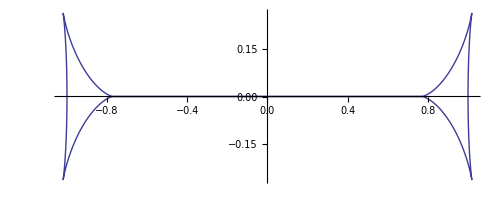

```mathematica
ParametricPlot[{Cos[psi]vs[psi,va,c0]-Sin[psi]vgst[psi,va,c0],Sin[psi]vs[psi,va,c0]+Cos[psi]vgst[psi,va,c0]}/.{va->1,c0->1.2},{psi,-π,π}]
```

```mathematica
vgs[psi_,va_,c0_]:={Cos[psi]vs[psi,va,c0]-Sin[psi]vgst[psi,va,c0],Sin[psi]vs[psi,va,c0]+Cos[psi]vgst[psi,va,c0]}
vgf[psi_,va_,c0_]:={Cos[psi]vf[psi,va,c0]-Sin[psi]vgft[psi,va,c0],Sin[psi]vf[psi,va,c0]+Cos[psi]vgft[psi,va,c0]}
vga[va_]:={{-va,0},{va,0}}
```

```mathematica
Manipulate[
range={{-√8,√8},{-√8,√8}};

Show[
{PolarPlot[vs[psi,va,c0]/.{va->b,c0->c},{psi,-π,π},PlotStyle->{{Red}},PlotRange->range],
PolarPlot[{-va Cos[psi],va Cos[psi]}/.{va->b,c0->c},{psi,-π,π},PlotStyle->{{Blue}},PlotRange->range],
PolarPlot[vf[psi,va,c0]/.{va->b,c0->c},{psi,-π,π},PlotStyle
->{{Green}},PlotRange->range]
},AspectRatio->1,Frame->True,
FrameLabel->{Subscript[v, z],Subscript[v, x]},
PlotLabel->"MHD Phase velocities",
ImageSize->{{320}},PlotRangePadding->None]

Show[
{ListPlot[vga[va]/.va->b,PlotRange->range],
ParametricPlot[{vgs[psi,va,c0]}/.{va->b,c0->c},{psi,-π,π},PlotRange->range,PlotStyle->{{Red}}],
ParametricPlot[{vgf[psi,va,c0]}/.{va->b,c0->c},{psi,-π,π},PlotRange->range,PlotStyle->{{Green}}]
},AspectRatio->1,Frame->True,
FrameLabel->{Subscript[v, z],Subscript[v, x]},
PlotLabel->"MHD Group velocities",
ImageSize->{{320}},PlotRangePadding->None]
,

{b,0.10000001,2},{c,0.01,2}]
```

```mathematica
Manipulate[
b=0.96824;
c=1.29099;
range={{-1,1},{-1,1}};

Show[
{PolarPlot[vs[psi,va,c0]*t/.{va->b,c0->c},{psi,-π,π},PlotStyle->{{Red}},PlotRange->range],
PolarPlot[{-va Cos[psi]*t,va Cos[psi]*t}/.{va->b,c0->c},{psi,-π,π},PlotStyle->{{Blue}},PlotRange->range],
PolarPlot[vf[psi,va,c0]*t/.{va->b,c0->c},{psi,-π,π},PlotStyle
->{{Green}},PlotRange->range]
},AspectRatio->1,Frame->True,
FrameLabel->{z,x},
PlotLabel->"MHD Phase position",
ImageSize->{{320}},PlotRangePadding->None]

Show[
{ListPlot[vga[va]*t/.va->b,PlotRange->range],
ParametricPlot[{vgs[psi,va,c0]*t}/.{va->b,c0->c},{psi,-π,π},PlotRange->range,PlotStyle->{{Red}}],
ParametricPlot[{vgf[psi,va,c0]*t}/.{va->b,c0->c},{psi,-π,π},PlotRange->range,PlotStyle->{{Green}}]
},AspectRatio->1,Frame->True,
FrameLabel->{z,x},
PlotLabel->"MHD Group position",
ImageSize->{{320}},PlotRangePadding->None]
,

{t,0.001,1}]
```

ListPlot::lpn: 0.001` vga[0.96824`] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[0.001` vga[0.96824`], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, AspectRatio → 1, Frame → True, « 10 » → « 1 », « 1 », ImageSize → {{320}}, PlotRangePadding → None].

ListPlot::lpn: 0.001` vga[0.96824`] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[0.001` vga[0.96824`], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, AspectRatio → 1, Frame → True, « 10 » → « 1 », « 1 », ImageSize → {{320}}, PlotRangePadding → None].

ListPlot::lpn: 0.001` vga[0.96824`] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[0.001` vga[0.96824`], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, AspectRatio → 1, Frame → True, « 10 » → « 1 », « 1 », ImageSize → {{320}}, PlotRangePadding → None].

ListPlot::lpn: 0.001` vga[0.96824`] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[0.001` vga[0.96824`], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, AspectRatio → 1, Frame → True, « 10 » → « 1 », « 1 », ImageSize → {{320}}, PlotRangePadding → None].

ListPlot::lpn: 0.001` vga[0.96824`] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[0.001` vga[0.96824`], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, AspectRatio → 1, Frame → True, « 10 » → « 1 », « 1 », ImageSize → {{320}}, PlotRangePadding → None].

ListPlot::lpn: 0.001` vga[0.96824`] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[0.001` vga[0.96824`], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], Skeleton[40]], List[]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}, AspectRatio → 1, Frame → True, « 10 » → « 1 », « 1 », ImageSize → {{320}}, PlotRangePadding → None].